# Векторные рисунки



```mathematica
Graphics[Circle[]]
```

## Графические примитивы

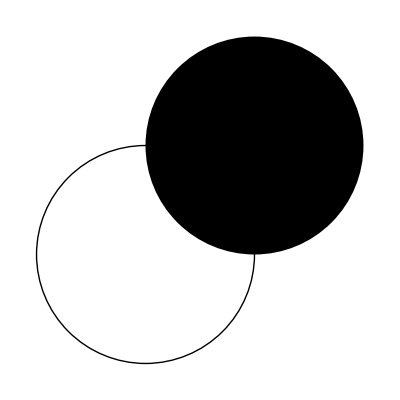

```mathematica
Graphics[{
Circle[{0,0},1],
Disk[{1,1},1]
}]
```

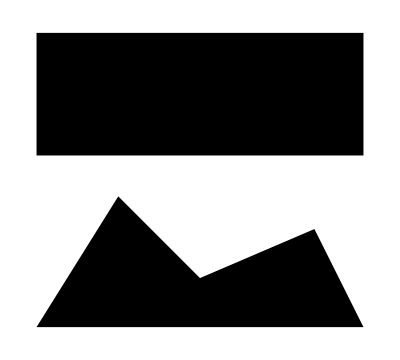

```mathematica
Graphics[{
Rectangle[{-1,.25},{1,1}],
Polygon[{{-1,-.8},{-.5,0},{0,-.5},{.7,-.2},{1,-.8}}]
}]
```

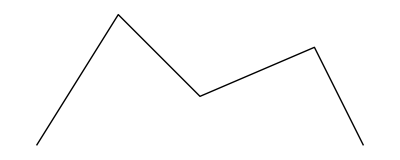

-Graphics-

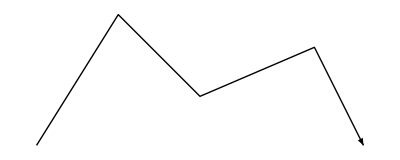

```mathematica
pts={{-1,-.8},{-.5,0},{0,-.5},{.7,-.2},{1,-.8}};
Graphics[{Line[pts]}]
Graphics[{Point[pts]}]
Graphics[{Arrow[pts]}]
```

```mathematica
Graphics[{
Line[{{-1,1},{1,1}}],
InfiniteLine[{{-1,0},{1,1}}],
InfiniteLine[{-1,0},{1,1}],
HalfLine[{{-.5,1},{1,-1}}]
},PlotRange->#{{-1,1},{-1,1}}]&/@{1.5,3,10}
```

{-Graphics-,-Graphics-,-Graphics-}

Circle[]
Disk[]
Rectangle[]
…
Polygon[]
Line[]
Point[]
…
InfiniteLine[]
HalfLine[]
Arrow[]
…

## Параметры примитивов

Цвет заливки

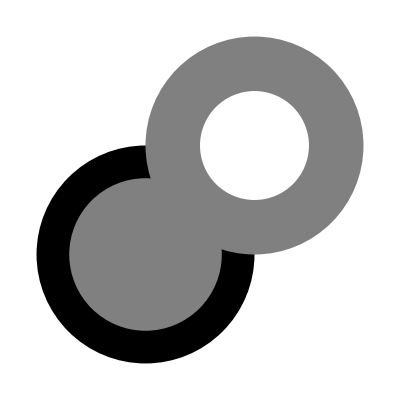

```mathematica
Graphics[{
Disk[{0,0},1],
Gray,
Disk[{0,0},.7],
Disk[{1,1},1],
White,
Disk[{1,1},.5]
}]
```

Группы

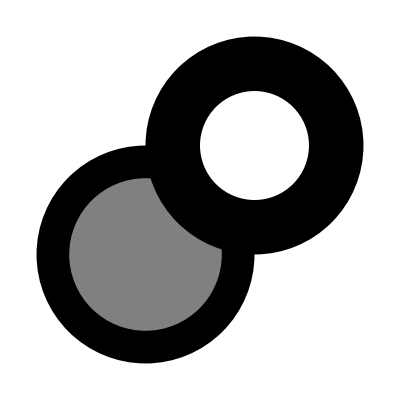

```mathematica
Graphics[{
Disk[{0,0},1],
{Gray,
Disk[{0,0},.7]},
Disk[{1,1},1],
White,
Disk[{1,1},.5]
}]
```

Порядок

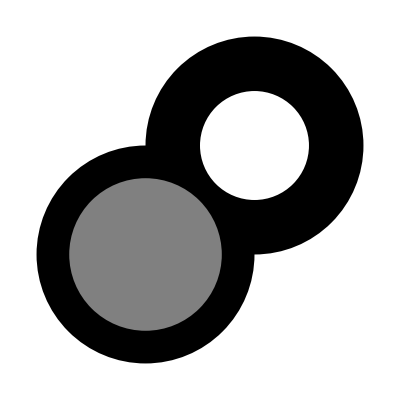

```mathematica
Graphics[{
Disk[{0,0},1],
Disk[{1,1},1],
Gray,
Disk[{0,0},.7],
White,
Disk[{1,1},.5]
}]
```

Параметры линий

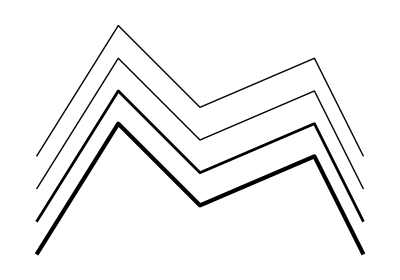

```mathematica
Graphics[{
Line[pts],
Thick,
Line[#-{0,.2}&/@pts],
AbsoluteThickness[2],
Line[#-2{0,.2}&/@pts],
AbsoluteThickness[3],
Line[#-3{0,.2}&/@pts]
}]
```

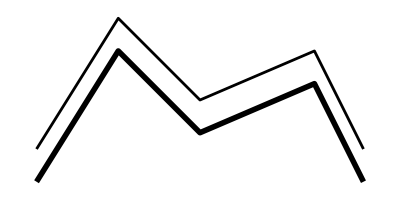
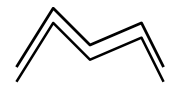
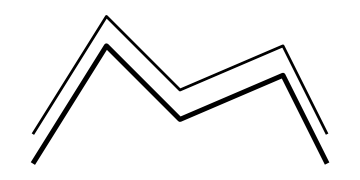

```mathematica
Graphics[{
AbsoluteThickness[2] (* значение в пикселях *),
Line[pts],
Thickness[.01] (* значение в долях от ширины рисунка *),
Line[#-{0,.2}&/@pts]
},ImageSize->#]&/@{Tiny,Small,Medium}
```

Thick
Thin
Thickness[]
AbsoluteThickness[]

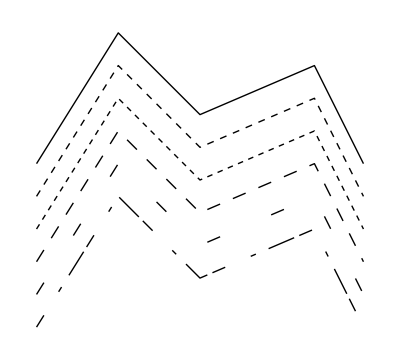

```mathematica
Graphics[{
Line[pts],
Dashed,
Line[#-{0,.2}&/@pts],
AbsoluteDashing[4],
Line[#-2{0,.2}&/@pts],
AbsoluteDashing[10],
Line[#-3{0,.2}&/@pts],
AbsoluteDashing[{10,40}],
Line[#-4{0,.2}&/@pts],
AbsoluteDashing[{10,20,4}],
Line[#-5{0,.2}&/@pts]
}]
```

Dashed
Dotted
DotDashed
Dashing[]
AbsoluteDashing[]
CapForm[]

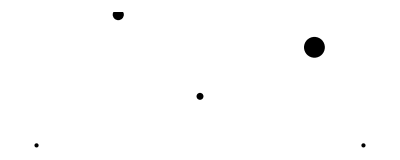

```mathematica
Graphics[{
Point[pts⟦1⟧],
PointSize[.02],
Point[pts⟦2⟧],
AbsolutePointSize[5],
Point[pts⟦3⟧],
AbsolutePointSize[15],
Point[pts⟦4⟧],
AbsolutePointSize[Large],
Point[pts⟦5⟧]
}]
```

Обводка

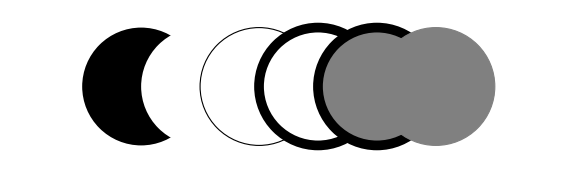

```mathematica
Graphics[{
Disk[{0,0},1],
White,
Disk[{1,0},1],
White,EdgeForm[{Black}],
Disk[{2,0},1],
EdgeForm[Directive[Black,AbsoluteThickness[7]]],
Disk[{3,0},1],
Gray,
Disk[{4,0},1],
EdgeForm[Dashing[1/8 π/8]],
Disk[{5,0},1]
},PlotRange->{{-1.5,6.5},1.2{-1,1}}]
```

Circle[] vs Disk[]

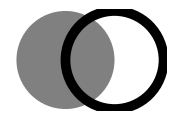

```mathematica
Graphics[{
Gray,
Disk[{0,0},1],
Directive[Black,AbsoluteThickness[7]],
Circle[{1,0},1]
},ImageSize->Small]
```

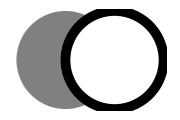

```mathematica
Graphics[{
Gray,
Disk[{0,0},1],
Directive[Black,AbsoluteThickness[7]]//EdgeForm,
White,Disk[{1,0},1]
},ImageSize->Small]
```

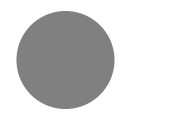

```mathematica
Graphics[{
Gray,
Disk[{0,0},1],
Directive[Black,AbsoluteThickness[7]]//EdgeForm,
Transparent,Disk[{1,0},1]
},ImageSize->Small]
```

```mathematica
Graphics[{
Gray,
Disk[{0,0},1],
White,
Disk[{1,0},1],
Directive[Black,AbsoluteThickness[7]],
Circle[{1,0},1]
},ImageSize->Small]
```

-Graphics-

Повороты

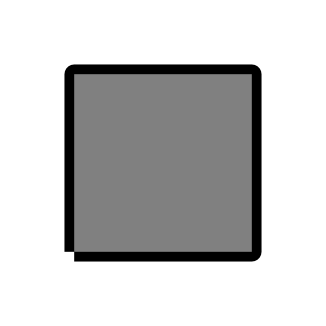

```mathematica
Graphics[{
{White,EdgeForm[Directive[AbsoluteThickness[14],Black]],Rectangle[{-1,-1},{1,1}]},
Gray,
Rectangle[{-1,-1},{1,1}]
},PlotRange->1.5{{-1,1},{-1,1}}]
```

```mathematica
Graphics[{
White,{EdgeForm[Directive[AbsoluteThickness[14],Black]],Rectangle[{-1,-1},{1,1}]},Rectangle[{-1,-1},{1,1}],
Gray,
Rotate[Rectangle[{-1,-1},{1,1}],π/5]
},PlotRange->1.5{{-1,1},{-1,1}}]
```

-Graphics-

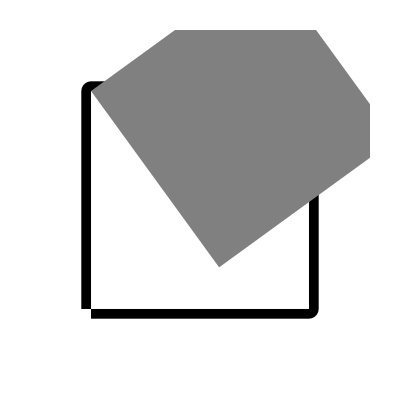

```mathematica
Graphics[{
White,{EdgeForm[Directive[AbsoluteThickness[14],Black]],Rectangle[{-1,-1},{1,1}]},Rectangle[{-1,-1},{1,1}],
Gray,
Rotate[Rectangle[{-1,-1},{1,1}],π/5,{-1,1}]
},PlotRange->1.5{{-1,1},{-1,1}}]
```

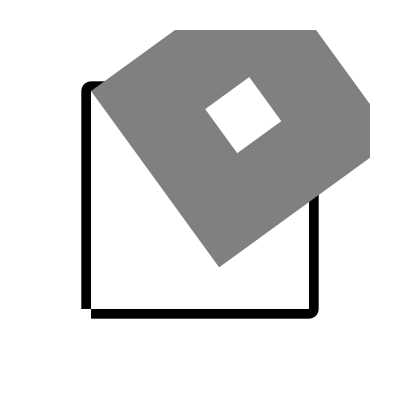

```mathematica
Graphics[{
White,{EdgeForm[Directive[AbsoluteThickness[14],Black]],Rectangle[{-1,-1},{1,1}]},Rectangle[{-1,-1},{1,1}],
Gray,
Rotate[{
Rectangle[{-1,-1},{1,1}],
White,Rectangle[.25{-1,-1},.25{1,1}]
},π/5,{-1,1}]
},PlotRange->1.5{{-1,1},{-1,1}}]
```

# Сопоставление с графиками

```mathematica
Plot[Sin[x],{x,0,10}]//FullForm
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[2.04082×10^-7,2.04082×10^-7],List[0.00306718,0.00306717],List[0.00613415,0.00613412],List[0.0122681,0.0122678],List[0.024536,0.0245335],List[0.0490718,0.0490521],List[0.0981434,0.0979859],List[0.196287,0.195029],List[0.409084,0.397769],List[0.607779,0.571045],List[0.610823,0.573541],List[0.613866,0.576032],List[0.619954,0.580997],List[0.632129,0.590863],List[0.656478,0.610331],List[0.705178,0.648169],List[0.802576,0.719149],List[0.805878,0.721439],List[0.80918,0.723721],List[0.815783,0.728263],List[0.82899,0.737249],List[0.855404,0.754836],List[0.908231,0.788417],List[0.911532,0.790443],List[0.914834,0.792461],List[0.921437,0.796472],List[0.934644,0.804388],List[0.961058,0.819798],List[1.01388,0.848892],List[1.01697,0.850516],List[1.02005,0.852133],List[1.02621,0.855342],List[1.03854,0.861662],List[1.06319,0.873909],List[1.11249,0.896802],List[1.11557,0.898161],List[1.11865,0.899512],List[1.12481,0.902187],List[1.13714,0.907435],List[1.16179,0.917516],List[1.21109,0.936001],List[1.21443,0.937171],List[1.21777,0.938331],List[1.22445,0.940619],List[1.23781,0.945069],List[1.26452,0.953463],List[1.26786,0.954465],List[1.2712,0.955455],List[1.27788,0.957405],List[1.29124,0.961177],List[1.31795,0.968204],List[1.32129,0.969034],List[1.32463,0.969853],List[1.33131,0.971459],List[1.34466,0.974541],List[1.348,0.975284],List[1.35134,0.976017],List[1.35802,0.977449],List[1.37138,0.980182],List[1.37472,0.980838],List[1.37806,0.981483],List[1.38474,0.982741],List[1.39809,0.985124],List[1.40143,0.985692],List[1.40477,0.98625],List[1.41145,0.987331],List[1.42481,0.989363],List[1.42809,0.989834],List[1.43137,0.990295],List[1.43792,0.991185],List[1.45104,0.992837],List[1.45431,0.993224],List[1.45759,0.993599],List[1.46415,0.994319],List[1.47726,0.995629],List[1.48054,0.99593],List[1.48382,0.99622],List[1.49038,0.996768],List[1.49366,0.997026],List[1.49693,0.997273],List[1.50349,0.997736],List[1.50677,0.997951],List[1.51005,0.998155],List[1.51333,0.998349],List[1.5166,0.998532],List[1.51988,0.998704],List[1.52316,0.998866],List[1.52972,0.999156],List[1.533,0.999286],List[1.53627,0.999404],List[1.53955,0.999512],List[1.54283,0.999609],List[1.54611,0.999695],List[1.54939,0.999771],List[1.55267,0.999836],List[1.55595,0.99989],List[1.55922,0.999933],List[1.5625,0.999966],List[1.56578,0.999987],List[1.56906,0.999998],List[1.57234,0.999999],List[1.57562,0.999988],List[1.57889,0.999967],List[1.58217,0.999935],List[1.58545,0.999893],List[1.58873,0.999839],List[1.59201,0.999775],List[1.59529,0.9997],List[1.59856,0.999614],List[1.60184,0.999518],List[1.60512,0.999411],List[1.6084,0.999293],List[1.61168,0.999164],List[1.61496,0.999025],List[1.61824,0.998875],List[1.62151,0.998714],List[1.62479,0.998543],List[1.62807,0.99836],List[1.63463,0.997963],List[1.63769,0.997764],List[1.64074,0.997555],List[1.64686,0.997109],List[1.64992,0.996872],List[1.65298,0.996625],List[1.65909,0.996104],List[1.66215,0.99583],List[1.66521,0.995546],List[1.67132,0.994951],List[1.68356,0.993649],List[1.68662,0.9933],List[1.68967,0.992942],List[1.69579,0.992199],List[1.70802,0.990599],List[1.71108,0.990176],List[1.71414,0.989744],List[1.72025,0.988852],List[1.73249,0.986957],List[1.73554,0.98646],List[1.7386,0.985954],List[1.74472,0.984914],List[1.75695,0.982723],List[1.78142,0.977902],List[1.78447,0.977258],List[1.78753,0.976605],List[1.79365,0.975271],List[1.80588,0.972495],List[1.83035,0.966506],List[1.83366,0.965649],List[1.83698,0.964782],List[1.84361,0.963017],List[1.85687,0.959358],List[1.8834,0.951535],List[1.88672,0.95051],List[1.89003,0.949475],List[1.89667,0.947372],List[1.90993,0.943043],List[1.93646,0.933887],List[1.93978,0.932696],List[1.94309,0.931495],List[1.94972,0.929062],List[1.96299,0.924074],List[1.98952,0.91361],List[2.04257,0.890762],List[2.04567,0.889351],List[2.04877,0.887931],List[2.05496,0.885066],List[2.06734,0.879235],List[2.09211,0.867168],List[2.14164,0.841447],List[2.2407,0.783881],List[2.24374,0.781993],List[2.24677,0.780098],List[2.25284,0.776286],List[2.26498,0.768577],List[2.28926,0.752819],List[2.33781,0.719983],List[2.43493,0.6493],List[2.64567,0.475844],List[2.84231,0.294838],List[3.05546,0.086031],List[3.26471,-0.122803],List[3.45986,-0.312917],List[3.67151,-0.505466],List[3.6746,-0.508127],List[3.67769,-0.510783],List[3.68386,-0.516081],List[3.69621,-0.526618],List[3.7209,-0.547448],List[3.77029,-0.588095],List[3.86907,-0.66499],List[3.87242,-0.667484],List[3.87576,-0.669971],List[3.88245,-0.674922],List[3.89583,-0.684734],List[3.92259,-0.703988],List[3.97611,-0.74097],List[3.97945,-0.743212],List[3.9828,-0.745446],List[3.98949,-0.749889],List[4.00287,-0.758672],List[4.02962,-0.775831],List[4.08314,-0.80847],List[4.08643,-0.810399],List[4.08971,-0.812318],List[4.09628,-0.816131],List[4.10941,-0.823651],List[4.13568,-0.838264],List[4.18823,-0.865743],List[4.19151,-0.867382],List[4.19479,-0.869012],List[4.20136,-0.872243],List[4.2145,-0.878592],List[4.24077,-0.890834],List[4.29331,-0.913465],List[4.29638,-0.914707],List[4.29944,-0.915941],List[4.30557,-0.918383],List[4.31782,-0.923163],List[4.34233,-0.932306],List[4.34539,-0.933409],List[4.34846,-0.934504],List[4.35458,-0.936668],List[4.36684,-0.940889],List[4.39135,-0.948907],List[4.39441,-0.949869],List[4.39747,-0.950823],List[4.4036,-0.952703],List[4.41586,-0.956355],List[4.44036,-0.963229],List[4.44343,-0.964047],List[4.44649,-0.964857],List[4.45262,-0.966449],List[4.46487,-0.969524],List[4.48938,-0.975237],List[4.4927,-0.975966],List[4.49602,-0.976684],List[4.50267,-0.978089],List[4.51595,-0.980769],List[4.51928,-0.981411],List[4.5226,-0.982043],List[4.52924,-0.983275],List[4.54253,-0.985608],List[4.54585,-0.986164],List[4.54917,-0.986709],List[4.55581,-0.987767],List[4.5691,-0.989752],List[4.57242,-0.99022],List[4.57574,-0.990678],List[4.58238,-0.991561],List[4.59567,-0.993196],List[4.59899,-0.993578],List[4.60231,-0.993948],List[4.60896,-0.994656],List[4.61228,-0.994993],List[4.6156,-0.99532],List[4.62224,-0.99594],List[4.62557,-0.996233],List[4.62889,-0.996516],List[4.63553,-0.997048],List[4.63885,-0.997297],List[4.64217,-0.997536],List[4.64882,-0.99798],List[4.65214,-0.998185],List[4.65546,-0.99838],List[4.65878,-0.998563],List[4.6621,-0.998736],List[4.66542,-0.998897],List[4.66875,-0.999048],List[4.67207,-0.999187],List[4.67539,-0.999316],List[4.67871,-0.999433],List[4.68203,-0.999539],List[4.68535,-0.999635],List[4.68867,-0.999719],List[4.692,-0.999792],List[4.69532,-0.999854],List[4.69864,-0.999905],List[4.70196,-0.999946],List[4.70506,-0.999973],List[4.70816,-0.999991],List[4.71126,-0.999999],List[4.71437,-0.999998],List[4.71747,-0.999987],List[4.72057,-0.999967],List[4.72367,-0.999936],List[4.72677,-0.999897],List[4.72987,-0.999847],List[4.73297,-0.999788],List[4.73607,-0.99972],List[4.73918,-0.999641],List[4.74228,-0.999553],List[4.74538,-0.999456],List[4.74848,-0.999349],List[4.75158,-0.999232],List[4.75468,-0.999106],List[4.75778,-0.99897],List[4.76399,-0.998669],List[4.76709,-0.998504],List[4.77019,-0.99833],List[4.77639,-0.997953],List[4.77949,-0.997749],List[4.78259,-0.997537],List[4.7888,-0.997082],List[4.8012,-0.996059],List[4.8043,-0.995779],List[4.8074,-0.99549],List[4.8136,-0.994882],List[4.82601,-0.993552],List[4.82911,-0.993196],List[4.83221,-0.99283],List[4.83841,-0.992069],List[4.85082,-0.990434],List[4.85392,-0.990001],List[4.85702,-0.989559],List[4.86322,-0.988646],List[4.87563,-0.986706],List[4.90044,-0.982371],List[4.90348,-0.981798],List[4.90652,-0.981216],List[4.9126,-0.980025],List[4.92476,-0.977534],List[4.94908,-0.972118],List[4.95212,-0.971401],List[4.95516,-0.970674],List[4.96125,-0.969195],List[4.97341,-0.966128],List[4.99773,-0.959566],List[5.00077,-0.958706],List[5.00381,-0.957837],List[5.00989,-0.956072],List[5.02205,-0.952436],List[5.04637,-0.944743],List[5.09502,-0.927686],List[5.09832,-0.926449],List[5.10162,-0.925203],List[5.10821,-0.922679],List[5.12141,-0.917512],List[5.14779,-0.9067],List[5.20057,-0.88319],List[5.20386,-0.881638],List[5.20716,-0.880077],List[5.21376,-0.876925],List[5.22695,-0.870508],List[5.25334,-0.85722],List[5.30611,-0.828864],List[5.30919,-0.827139],List[5.31227,-0.825405],List[5.31842,-0.821914],List[5.33073,-0.814839],List[5.35536,-0.800319],List[5.40461,-0.769833],List[5.5031,-0.70334],List[5.50644,-0.700965],List[5.50977,-0.698582],List[5.51644,-0.693792],List[5.52979,-0.684121],List[5.55647,-0.664415],List[5.60985,-0.623597],List[5.7166,-0.536754],List[5.9262,-0.349449],List[6.1217,-0.160782],List[6.33371,0.0505068],List[6.53162,0.24589],List[6.72563,0.428154],List[6.93616,0.60755],List[6.93923,0.609984],List[6.9423,0.612413],List[6.94843,0.617254],List[6.96071,0.626866],List[6.98526,0.645805],List[7.03437,0.682503],List[7.03744,0.684743],List[7.04051,0.686977],List[7.04664,0.691424],List[7.05892,0.700241],List[7.08347,0.717556],List[7.13258,0.750879],List[7.1359,0.753072],List[7.13923,0.755257],List[7.14589,0.759602],List[7.15919,0.76819],List[7.18581,0.784956],List[7.23904,0.816809],List[7.24237,0.818724],List[7.2457,0.82063],List[7.25235,0.824414],List[7.26566,0.831873],List[7.29228,0.846348],List[7.34551,0.873489],List[7.34862,0.874997],List[7.35172,0.876497],List[7.35794,0.879471],List[7.37036,0.885318],List[7.39522,0.8966],List[7.39832,0.897971],List[7.40143,0.899334],List[7.40764,0.902034],List[7.42007,0.907328],List[7.44492,0.917496],List[7.44803,0.918727],List[7.45114,0.91995],List[7.45735,0.922368],List[7.46978,0.927097],List[7.49463,0.936125],List[7.54434,0.952442],List[7.54738,0.953366],List[7.55043,0.954281],List[7.55652,0.956084],List[7.5687,0.959584],List[7.59307,0.966156],List[7.59612,0.966937],List[7.59916,0.967709],List[7.60525,0.969227],List[7.61744,0.972154],List[7.6418,0.977575],List[7.64485,0.978212],List[7.6479,0.978839],List[7.65399,0.980068],List[7.66617,0.982415],List[7.66922,0.982979],List[7.67226,0.983534],List[7.67835,0.984617],List[7.69054,0.986673],List[7.69358,0.987164],List[7.69663,0.987646],List[7.70272,0.988582],List[7.7149,0.990344],List[7.71795,0.990762],List[7.721,0.99117],List[7.72709,0.99196],List[7.73927,0.993428],List[7.74257,0.993801],List[7.74588,0.994162],List[7.75249,0.994854],List[7.75579,0.995183],List[7.75909,0.995501],List[7.7657,0.996106],List[7.769,0.996392],List[7.77231,0.996667],List[7.77892,0.997184],List[7.78222,0.997426],List[7.78552,0.997658],List[7.79213,0.998088],List[7.79543,0.998287],List[7.79874,0.998474],List[7.80204,0.998651],List[7.80535,0.998818],List[7.80865,0.998973],List[7.81195,0.999117],List[7.81526,0.99925],List[7.81856,0.999373],List[7.82187,0.999484],List[7.82517,0.999585],List[7.82847,0.999675],List[7.83178,0.999753],List[7.83508,0.999821],List[7.83838,0.999878],List[7.84169,0.999924],List[7.84499,0.99996],List[7.8483,0.999984],List[7.8516,0.999997],List[7.8549,1.],List[7.85821,0.999991],List[7.86151,0.999972],List[7.86481,0.999941],List[7.86812,0.9999],List[7.87142,0.999848],List[7.87473,0.999785],List[7.87803,0.999711],List[7.88133,0.999626],List[7.88464,0.99953],List[7.88794,0.999423],List[7.89124,0.999306],List[7.89455,0.999177],List[7.89785,0.999038],List[7.90116,0.998887],List[7.90446,0.998726],List[7.91107,0.998371],List[7.91437,0.998177],List[7.91767,0.997972],List[7.92428,0.99753],List[7.92759,0.997292],List[7.93089,0.997044],List[7.9375,0.996515],List[7.95071,0.995325],List[7.9538,0.995023],List[7.95688,0.994711],List[7.96305,0.994058],List[7.97538,0.99264],List[7.97846,0.992262],List[7.98155,0.991875],List[7.98771,0.991071],List[8.00005,0.989351],List[8.00313,0.988898],List[8.00621,0.988435],List[8.01238,0.987481],List[8.02472,0.98546],List[8.04938,0.98097],List[8.05247,0.980366],List[8.05555,0.979754],List[8.06172,0.9785],List[8.07405,0.975882],List[8.09872,0.970201],List[8.1018,0.969449],List[8.10489,0.968688],List[8.11105,0.967139],List[8.12339,0.96393],List[8.14805,0.957072],List[8.1514,0.956098],List[8.15474,0.955113],List[8.16142,0.953112],List[8.17478,0.948982],List[8.20152,0.940215],List[8.20486,0.939072],List[8.2082,0.937918],List[8.21488,0.935579],List[8.22825,0.930776],List[8.25498,0.920672],List[8.25832,0.919363],List[8.26166,0.918043],List[8.26834,0.915373],List[8.28171,0.90991],List[8.30844,0.898498],List[8.3619,0.873756],List[8.36519,0.872156],List[8.36847,0.870547],List[8.37503,0.867299],List[8.38815,0.860693],List[8.41439,0.847036],List[8.46688,0.817983],List[8.57186,0.753204],List[8.57492,0.751187],List[8.57798,0.749164],List[8.5841,0.745096],List[8.59634,0.736876],List[8.62082,0.720107],List[8.66978,0.685284],List[8.76771,0.610797],List[8.98007,0.430191],List[9.17833,0.243957],List[9.3727,0.0520572],List[9.58357,-0.158127],List[9.78034,-0.34812],List[9.78378,-0.351336],List[9.78721,-0.354547],List[9.79407,-0.360957],List[9.8078,-0.373725],List[9.83526,-0.399049],List[9.89017,-0.448774],List[9.8936,-0.451839],List[9.89704,-0.454898],List[9.9039,-0.461],List[9.91763,-0.473139],List[9.94509,-0.497147],List[9.94852,-0.500122],List[9.95195,-0.503091],List[9.95881,-0.509012],List[9.97254,-0.52078],List[9.97597,-0.523707],List[9.97941,-0.526628],List[9.98627,-0.532451],List[9.9897,-0.535353],List[9.99314,-0.538249],List[9.99657,-0.541138],List[10.,-0.544021]]]],"Charting`Private`Tag$2337#1"]]],List[],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]],List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,10],List[-0.999999,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]



```mathematica
Plot[Sin[x],{x,0,10}]
```

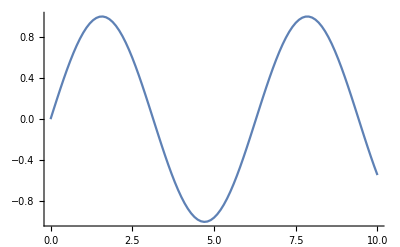

```mathematica
Graphics[{
{RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6],Line[{#,Sin[#]}&/@Range[0,10,.1]]}
},PlotRange->{{0,10},{-1,1}},PlotRangePadding->Scaled[.05],AspectRatio->1/GoldenRatio,Axes->True]
```

Замена графических выражений в графиках

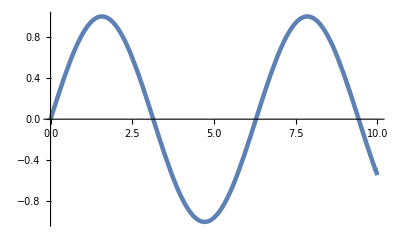

```mathematica
Plot[Sin[x],{x,0,10}]/.Line->Arrow/.AbsoluteThickness[__]->Thickness[.008]
```

Встраивание графиков в рисунки

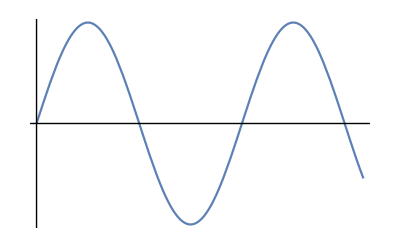

```mathematica
Graphics[{
InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],
Plot[Sin[x],{x,0,10}]⟦1⟧
},PlotRange->{{0,10},{-1,1}},PlotRangePadding->Scaled[.05],AspectRatio->1/GoldenRatio]
```

Встраивание рисунков в графики

```mathematica
Plot[Sin[x],{x,0,10},
Prolog->{Dashed,Gray,HalfLine[{0,1},{1,0}],InfiniteLine[{π/2,0},{0,1}]},
Epilog->{AbsolutePointSize[5],Point[{π/2,1}]}
]
```

-Graphics-

Prolog — группа графических выражений,встраиваемая до основного графика
Epilog — группа графических выражений,встраиваемая после основного графика

Prolog vs Epilog

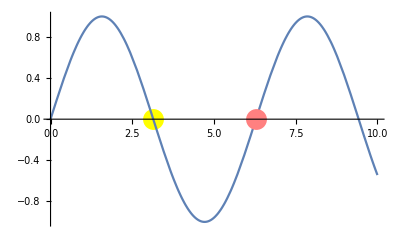

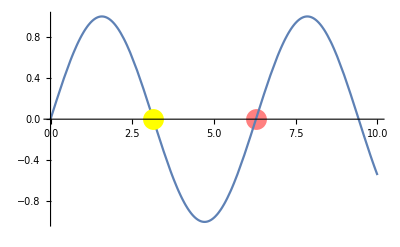

```mathematica
Plot[Sin[x],{x,0,10},
Prolog->{Yellow,AbsolutePointSize[15],Point[{π,0}]},
Epilog->{Pink,AbsolutePointSize[15],Point[{2π,0}]}
]
Plot[Sin[x],{x,0,10},
Epilog->{Yellow,AbsolutePointSize[15],Point[{π,0}]},
Prolog->{Pink,AbsolutePointSize[15],Point[{2π,0}]}
]
```

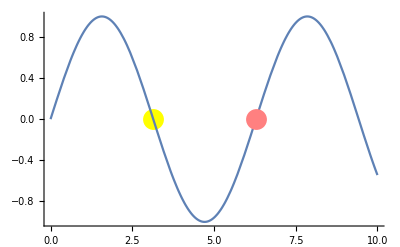

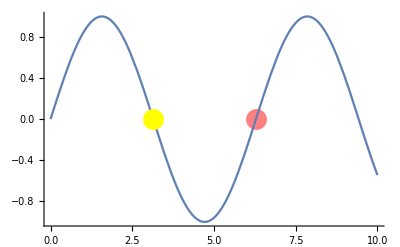

```mathematica
Graphics[{
{Yellow,AbsolutePointSize[15],Point[{π,0}]},
Plot[Sin[x],{x,0,10}]⟦1⟧,
{Pink,AbsolutePointSize[15],Point[{2π,0}]}
},AspectRatio->1/GoldenRatio,Axes->True]
Graphics[{
{Pink,AbsolutePointSize[15],Point[{2π,0}]},
Plot[Sin[x],{x,0,10}]⟦1⟧,
{Yellow,AbsolutePointSize[15],Point[{π,0}]}
},AspectRatio->1/GoldenRatio,Axes->True]
```

# Цвета

```mathematica
Red//FullForm
```

RGBColor[1,0,0]

```mathematica
RGBColor[1,0,0]
```

RGBColor[1, 0, 0]

```mathematica
RGBColor[1,.5,0]
RGBColor[1,1,0]
```

RGBColor[1, 0.5, 0]

RGBColor[1, 1, 0]

```mathematica
RGBColor["#ff0088"]
RGBColor["#bada55"]
```

RGBColor[1., 0., 0.5333333333333333]

RGBColor[0.7294117647058823, 0.8549019607843137, 0.3333333333333333]

Выбор цветов

-Graphics-

```mathematica
Purple
Darker[Purple]
Lighter[Purple]
Lighter[Purple,.75]
```

RGBColor[0.5, 0, 0.5]

RGBColor[0.33333333333333337, 0, 0.33333333333333337]

RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666]

RGBColor[0.875, 0.75, 0.875]

```mathematica
Blend[{Purple,Yellow},0]
Blend[{Purple,Yellow},.5]
Blend[{Purple,Yellow},1]
```

RGBColor[0.5, 0, 0.5]

RGBColor[0.75, 0.5, 0.25]

RGBColor[1, 1, 0]

```mathematica
Graphics[{Thickness[.025],
{Blend[{RGBColor[0.5, 0, 0.5],RGBColor[1, 1, 0]},1-#],
Circle[{-.9#,0},#]}&/@Range[1,0,-.1]
}]
```

-Graphics-

```mathematica
Black//FullForm
```

GrayLevel[0]

```mathematica
GrayLevel[0]
GrayLevel[0.5]
GrayLevel[1]
```

GrayLevel[0]

GrayLevel[0.5]

GrayLevel[1]

Прозрачность

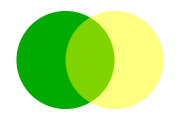

```mathematica
Graphics[{
RGBColor[0, Rational[2, 3], 0],Disk[],
RGBColor[1, 1, 0],Opacity[.5],Disk[{1,0}]
},ImageSize->Small]
```

```mathematica
Graphics[{
RGBColor[0, Rational[2, 3], 0],Disk[],
Opacity[.5,RGBColor[1, 1, 0]],Disk[{1,0}]
},ImageSize->Small]
```

-Graphics-

# Параметрическая анимация

```mathematica
Pic[φ_]:=Graphics[{
Circle[],Disk[{Cos[φ],Sin[φ]}-.4{Cos[4φ],-Sin[4φ]},.2]
},PlotRange->1.75{{-1,1},{-1,1}}];

Animate[Pic[2π t],{t,0,1}]
```

Manipulate[]
Animate[]
ListAnimate[]

Dynamic[]
Manipulator[]
Animator[]